# 1.4

```mathematica
OTCdata={11.88,6.27,5.49,4.81,4.40,3.78,3.44,3.11,2.88,2.68,7.99,6.07,5.26,4.79,4.05,3.69,3.36,3.03,2.74,2.63,7.15,5.98,5.07
,4.55,3.94,3.62,3.26,2.99,2.74,2.62,7.13,5.91,4.94,4.43,3.93,3.48,3.20,2.89,2.69,2.61};
```

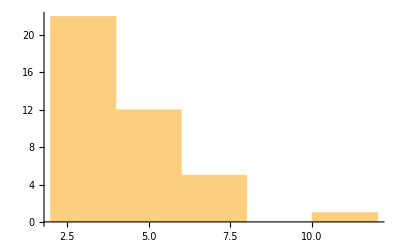

```mathematica
Histogram[OTCdata]
```

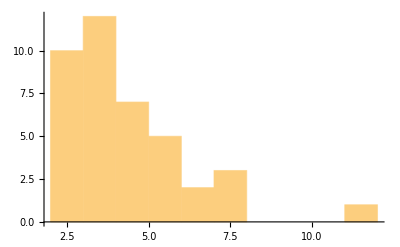

```mathematica
Histogram[OTCdata,"Sturges"]
```

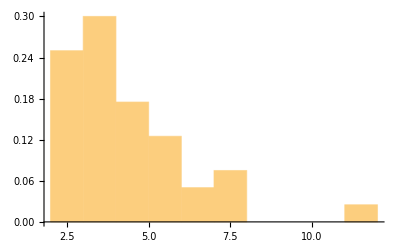

```mathematica
Histogram[OTCdata,"Sturges","Probability"]
```

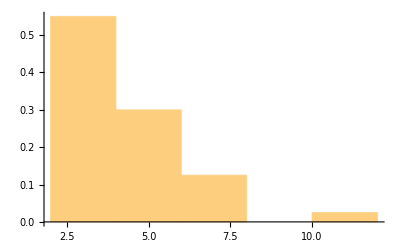

```mathematica
Histogram[OTCdata,Automatic,"Probability"]
```

```mathematica
Select[#>4&][OTCdata]
```

{11.88,6.27,5.49,4.81,4.4,7.99,6.07,5.26,4.79,4.05,7.15,5.98,5.07,4.55,7.13,5.91,4.94,4.43}

```mathematica
Length[Select[#>4&][OTCdata]]/Length[OTCdata]
```

9/20

```mathematica
N[Length[Select[#>4&][OTCdata]]/Length[OTCdata]]
```

0.45

```mathematica
Probability[x<5,x\[Distributed]OTCdata]
```

29/40

```mathematica
N[Probability[x<5,x\[Distributed]OTCdata]]
```

0.725

## 1.16

```mathematica
OTCdata
```

{11.88,6.27,5.49,4.81,4.4,3.78,3.44,3.11,2.88,2.68,7.99,6.07,5.26,4.79,4.05,3.69,3.36,3.03,2.74,2.63,7.15,5.98,5.07,4.55,3.94,3.62,3.26,2.99,2.74,2.62,7.13,5.91,4.94,4.43,3.93,3.48,3.2,2.89,2.69,2.61}

```mathematica
OUTLIERELIMINATED=Rest[OTCdata]
```

{6.27,5.49,4.81,4.4,3.78,3.44,3.11,2.88,2.68,7.99,6.07,5.26,4.79,4.05,3.69,3.36,3.03,2.74,2.63,7.15,5.98,5.07,4.55,3.94,3.62,3.26,2.99,2.74,2.62,7.13,5.91,4.94,4.43,3.93,3.48,3.2,2.89,2.69,2.61}

```mathematica
Mean[OTCdata]
```

4.387

```mathematica
Mean[OUTLIERELIMINATED]
```

4.19487

```mathematica
StandardDeviation[OUTLIERELIMINATED]
```

1.44182

```mathematica
Select[Abs[#-Mean[OUTLIERELIMINATED]]<StandardDeviation[OUTLIERELIMINATED]&][OUTLIERELIMINATED]
```

{5.49,4.81,4.4,3.78,3.44,3.11,2.88,5.26,4.79,4.05,3.69,3.36,3.03,5.07,4.55,3.94,3.62,3.26,2.99,4.94,4.43,3.93,3.48,3.2,2.89}

```mathematica
Length[Select[Abs[#-Mean[OUTLIERELIMINATED]]<StandardDeviation[OUTLIERELIMINATED]&][OUTLIERELIMINATED]]
```

25

```mathematica
Length[Select[Abs[#-Mean[OUTLIERELIMINATED]]<StandardDeviation[OUTLIERELIMINATED]&][OUTLIERELIMINATED]]/Length[OUTLIERELIMINATED]//N
```

0.641026

```mathematica
Length[Select[Abs[#-Mean[OUTLIERELIMINATED]]<2StandardDeviation[OUTLIERELIMINATED]&][OUTLIERELIMINATED]]
```

36

```mathematica
Length[Select[Abs[#-Mean[OUTLIERELIMINATED]]<2StandardDeviation[OUTLIERELIMINATED]&][OUTLIERELIMINATED]]/Length[OUTLIERELIMINATED]//N
```

0.923077

```mathematica
Length[Select[Abs[#-Mean[OUTLIERELIMINATED]]<3StandardDeviation[OUTLIERELIMINATED]&][OUTLIERELIMINATED]]
```

39

```mathematica
Length[Select[Abs[#-Mean[OUTLIERELIMINATED]]<3StandardDeviation[OUTLIERELIMINATED]&][OUTLIERELIMINATED]]/Length[OUTLIERELIMINATED]//N
```

1.

```mathematica
StandardDeviation[OTCdata]
```

1.87138

```mathematica
Length[Select[Abs[#-Mean[OTCdata]]<StandardDeviation[OTCdata]&][OTCdata]]/Length[OTCdata]//N
```

0.875

```mathematica
Length[Select[Abs[#-Mean[OTCdata]]<2StandardDeviation[OTCdata]&][OTCdata]]/Length[OTCdata]//N
```

0.975

```mathematica
Length[Select[Abs[#-Mean[OTCdata]]<3StandardDeviation[OTCdata]&][OTCdata]]/Length[OTCdata]//N
```

0.975

## 1.21

```mathematica
Probability[x>20,x\[Distributed]NormalDistribution[22,2]]
```

1/2 (1+Erf[1/(√2)])

```mathematica
NProbability[x>20,x\[Distributed]NormalDistribution[22,2]]
```

0.841345

## 1.29

```mathematica
NProbability[x>3.02∨x<2.98,x\[Distributed]NormalDistribution[300,0.01]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.

```mathematica
NProbability[x>3.02∨x<2.98,x\[Distributed]NormalDistribution[3,0.01]]
```

0.0455003